```mathematica
ClearAll[files, importfile, raw]
```

```mathematica
files=FileNames["*.xlsx",NotebookDirectory[]]
```

{/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/331/Книга1.xlsx,/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/331/1.xlsx,/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/331/2.xlsx,/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/331/3.xlsx,/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/331/~$Книга1.xlsx,/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/331/~$1.xlsx,/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/331/~$2.xlsx,/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/331/~$3.xlsx}

```mathematica
importfile = files⟦4⟧
```

/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/331/3.xlsx

```mathematica
raw = Import[importfile];
```

```mathematica
makeAssoc[header_][row_]:=<|header->row//Thread|>;
makeDataset@raw_:=With[{header=raw⟦1⟧,data=raw⟦2;;⟧},
makeAssoc@header/@data
]//Dataset;
```

## Dataset1

```mathematica
dataset1=makeDataset[raw⟦1⟧]
```

Dataset[<>]

```mathematica
dataset1WithErrs=dataset1[All,<|"B"->(Around[#B,#dB]&),"I"->(Around[#I,#dI]&)|>]
```

Dataset[<>]

## Dataset2

```mathematica
dataset2=makeDataset[raw⟦2⟧]
```

Dataset[<>]

```mathematica
dataset2WithErrs=dataset2[All,<|"B"->(Around[#B,#dB]&),"I"->(Around[#I,#dI]&)|>]
```

Dataset[<>]

## Dataset3

```mathematica
dataset3=makeDataset[raw⟦3⟧]
```

Dataset[<>]

```mathematica
dataset3WithErrs=dataset3[All,<|"B"->(Around[#B,#dB]&),"I"->(Around[#I,#dI]&)|>]
```

Dataset[<>]

## Dataset4

```mathematica
dataset4=makeDataset[raw⟦4⟧]
```

Dataset[<>]

```mathematica
dataset4WithErrs=dataset4[All,<|"B"->(Around[#B,#dB]&),"I"->(Around[#I,#dI]&)|>]
```

Dataset[<>]

## Dataset5

```mathematica
dataset5=makeDataset[raw⟦5⟧]
```

Dataset[<>]

```mathematica
dataset5WithErrs=dataset5[All,<|"B"->(Around[#B,#dB]&),"I"->(Around[#I,#dI]&)|>]
```

Dataset[<>]

```mathematica
ClearAll[x,y]
```

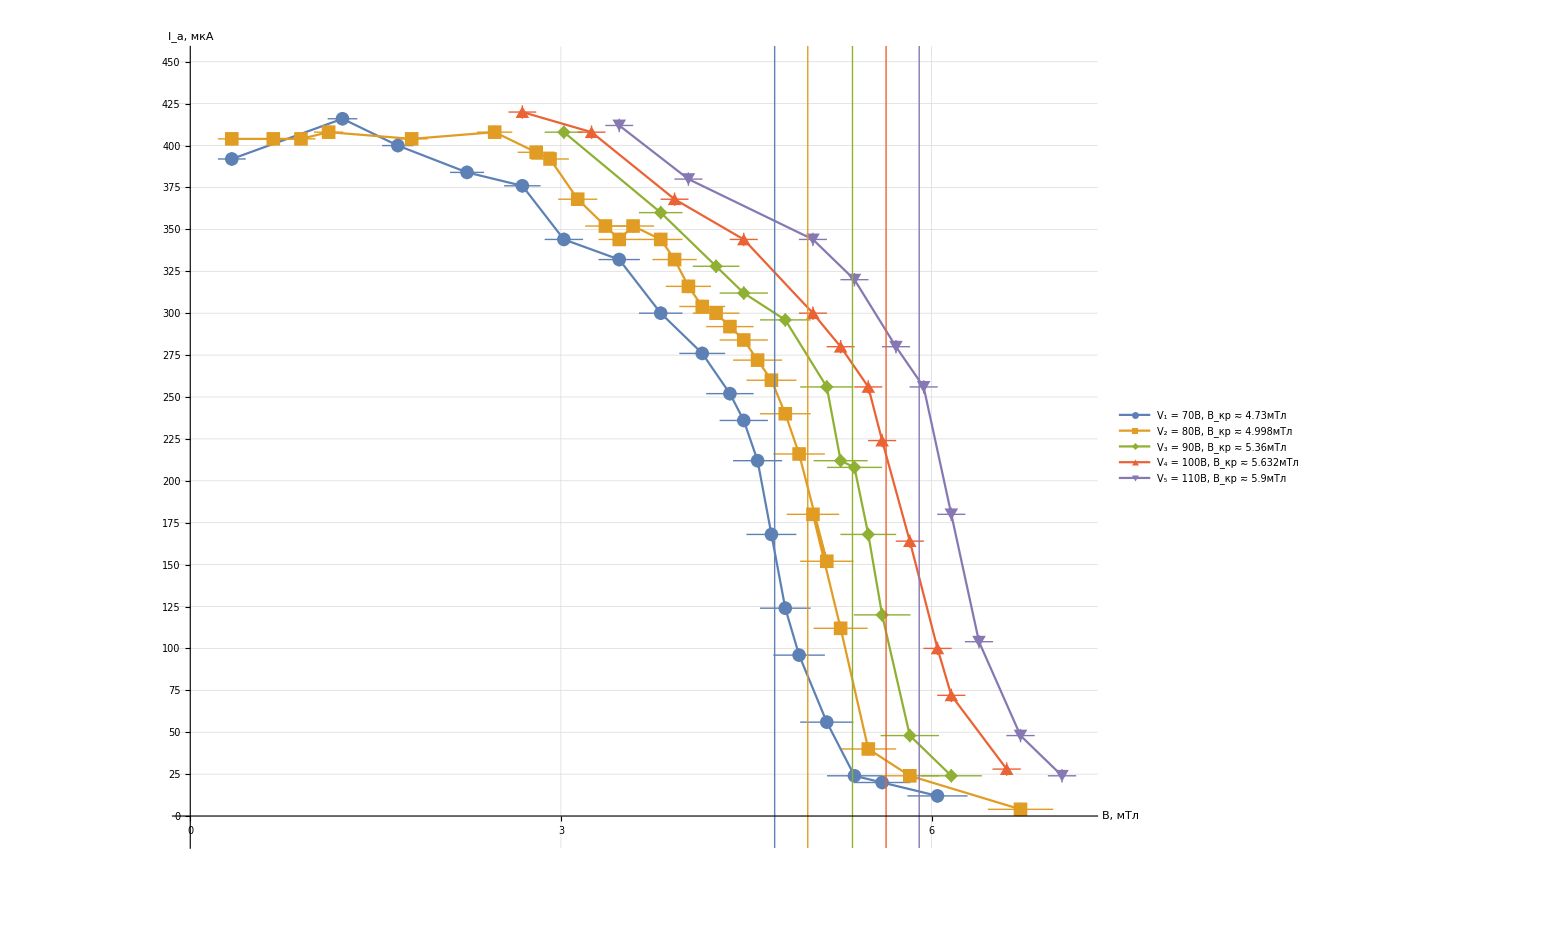

```mathematica
Show[
ListPlot[{dataset1WithErrs,dataset2WithErrs,dataset3WithErrs,dataset4WithErrs,dataset5WithErrs},
AxesLabel->{Style["B, мТл",Large],Style["I_(:0430), мкА",Large]},
AxesStyle->Directive[Arrowheads[{0.02}],Black], 
ImageSize->1500,
GridLines->{Range[0,430,0.125.00], Range[0,500,12.5]},
Ticks-> {Range[0,420,1],Range[0,500,25]}, 
TicksStyle->20,
Joined->True,
(*InterpolationOrder->4,*)
(*PlotStyle->Thickness[0.001]*)
PlotRange->{{0,7.2},{-10,450}},
PlotMarkers->{Automatic,14},
PlotLegends->Placed[LineLegend[
Automatic,
{"V_1 = 70B,  B_(:043a:0440) ≂ 4.73мТл","V_2 = 80B,  B_(:043a:0440) ≂ 4.998мТл","V_3 = 90B,  B_(:043a:0440) ≂ 5.36мТл","V_4 = 100B,  B_(:043a:0440) ≂ 5.632мТл","V_5 = 110B,  B_(:043a:0440) ≂ 5.9мТл"},
LegendMarkerSize->15,
LegendFunction->Framed,
LabelStyle->{FontSize->18},
LegendLayout->"Column"
],
{Scaled[0.2],Scaled[0.4]}
]
],
Graphics[{{RGBColor["#5f82b5"],Thick,Line[{{4.73,-100},{4.73,1000}}]}, (* 9 точек, начиная с -3 *)
{RGBColor["#e09c24"],Thick, Line[{{4.998,-100},{4.998.00,1000}}]}, (* 8 точек, начиная с -3  *)
{RGBColor["#8fb031"],Thick, Line[{{5.36,-100},{5.36.00,1000}}]}, (* 7 точек, начиная с -2 *)
{RGBColor["#ec6235"],Thick, Line[{{5.632,-100},{5.632.00,1000}}]}, (* .007 точке, начиная с -2 *)
{RGBColor["#8778b2"],Thick, Line[{{5.9,-100},{5.9,1000}}]}}] (* 7 точке, начиная с -2 *)
]
```

## Newdataset

```mathematica
ClearAll[files, importfile, raw,x,y]
```

```mathematica
files=FileNames["*.xlsx",NotebookDirectory[]]
```

{/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/331/Книга1.xlsx,/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/331/1.xlsx,/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/331/2.xlsx,/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/331/3.xlsx,/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/331/4.xlsx,/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/331/~$Книга1.xlsx,/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/331/~$1.xlsx,/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/331/~$3.xlsx,/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/331/~$4.xlsx}

```mathematica
importfile = files⟦5⟧
```

/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/331/4.xlsx

```mathematica
raw = Import[importfile];
```

```mathematica
dataset6=makeDataset[raw⟦1⟧]
```

Dataset[<>]

```mathematica
dataset6WithErrs=dataset6[All,<|"V"->(Around[#V,#dV]&),"B2"->(Around[#B2,#dB2]&)|>]
```

Dataset[<>]

```mathematica
ClearAll[line6]
```

```mathematica
line6 =LinearModelFit[Normal@dataset6[All,{"V","B2"}/*Values],{0,x},x]
```

LinearModelFit::rank: The rank of the design matrix 1 is less than the number of terms 2 in the model. The model and results based upon it may contain significant numerical error.

FittedModel[0.+0.316897 x]

```mathematica
line6["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
0 | 0. | 0. | ComplexInfinity | 0.
x | 0.316897 | 0.001333 | 237.732 | 1.64128×10^-7

```mathematica
line7 =LinearModelFit[Normal@dataset6[All,{"V","B2"}/*Values],{0,x},x]
```

LinearModelFit::rank: The rank of the design matrix 1 is less than the number of terms 2 in the model. The model and results based upon it may contain significant numerical error.

FittedModel[0.+0.316897 x]

```mathematica
Show[
Plot[
{line@x},
AxesLabel->{Style["V_(:0430), B",Large],Style["(B_(:043a:0440))^2, (мТл)^2",Large]},
AxesStyle->Directive[Arrowheads[{0.02}],Black], 
ImageSize->1500,
GridLines->{Range[0,430,2.00], Range[0,500,2]},
Ticks-> {Range[0,420,5],Range[0,500,2]}, 
TicksStyle->20,
(*InterpolationOrder->4,*)
(*PlotStyle->Thickness[0.001]*)
PlotRange->{{0,120},{0,39}},
PlotMarkers->{Automatic,14},
PlotLegends->Placed[LineLegend[
Automatic,
{"V_1 = 70B,  B_(:043a:0440) ≂ 4.73мТл","V_2 = 80B,  B_(:043a:0440) ≂ 4.998мТл","V_3 = 90B,  B_(:043a:0440) ≂ 5.36мТл","V_4 = 100B,  B_(:043a:0440) ≂ 5.632мТл","V_5 = 110B,  B_(:043a:0440) ≂ 5.9мТл"},
LegendMarkerSize->15,
LegendFunction->Framed,
LabelStyle->{FontSize->18},
LegendLayout->"Column"
],
{Scaled[0.2],Scaled[0.4]}
]
]
]
```

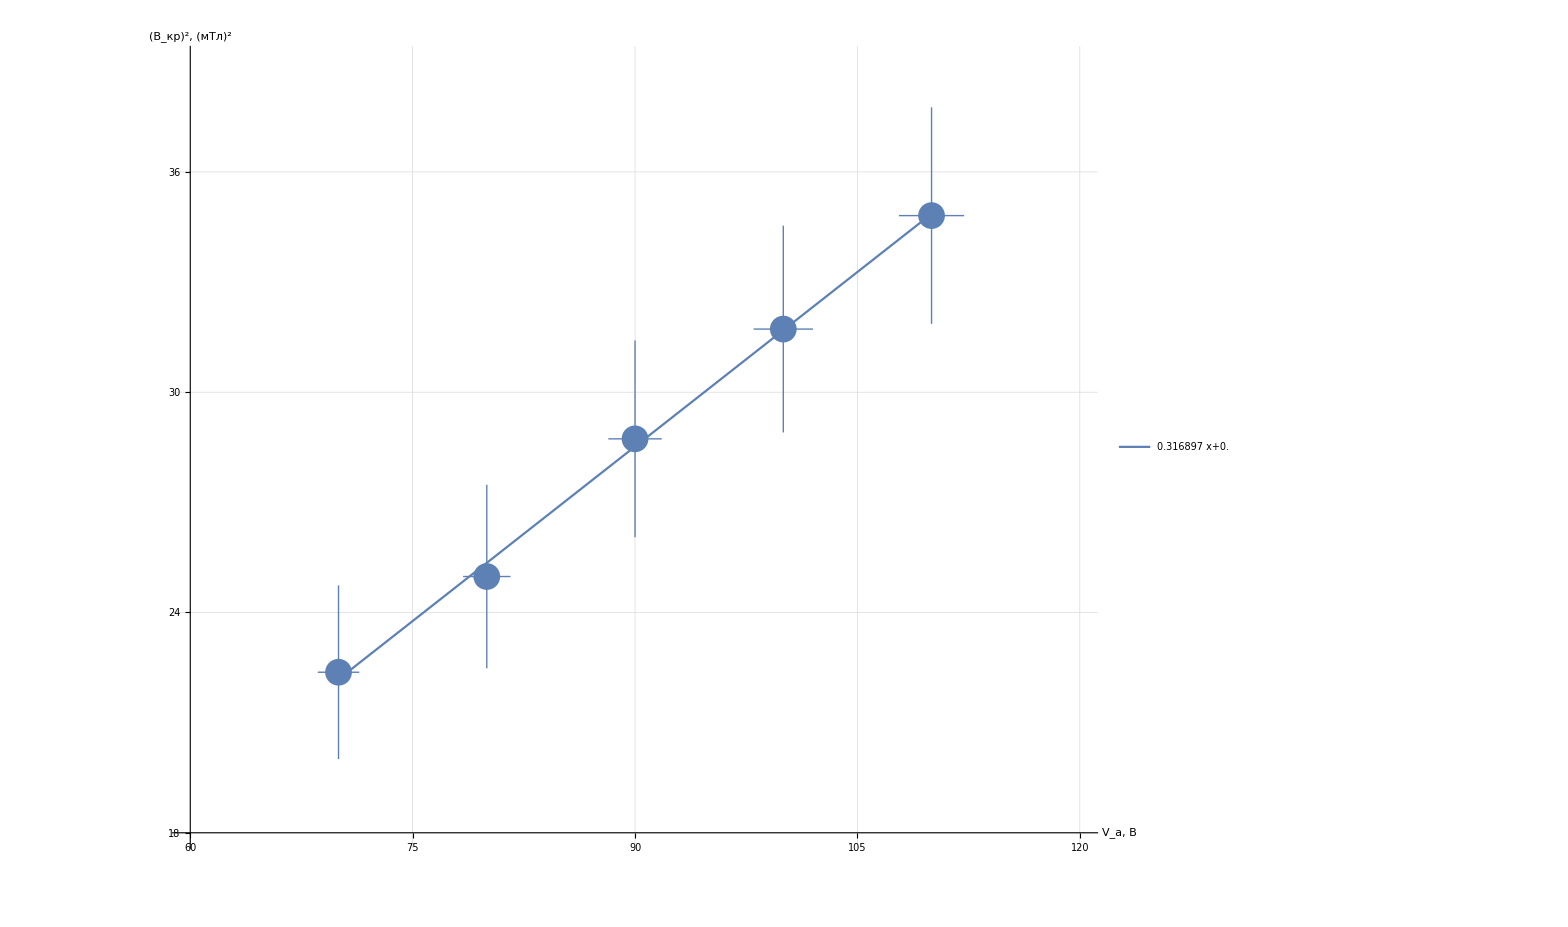

```mathematica
Show[
Plot[
{line6@x},
{x,70, 110},
AxesLabel->{Style["V_(:0430), B",Large],Style["(B_(:043a:0440))^2, (мТл)^2",Large]},
AxesStyle->Directive[Arrowheads[{0.02}],Black], 
ImageSize->1500,
GridLines->{Range[0,430,1], Range[0,500,1]},
Ticks-> {Range[0,420,5],Range[0,500,2]}, 
TicksStyle->20,
PlotRange->{{60,120},{18,39}},
PlotLegends->Placed[
LineLegend[
{Normal@line6},
LabelStyle->20
],
{Scaled[0.2],Scaled[0.75]}
]
],
ListPlot[
{dataset6WithErrs}
]
]
```

```mathematica
Show[
Plot[
{line@x},
{x,0.59, 3},
AxesLabel->{Style["I, A", Large],Style["B_(:0444), мТл",Large]},
ImageSize->1200,
AxesStyle->Directive[Arrowheads[{0.02}],Black],
GridLines-> {Range[0,4,0.1],Range[0,15,1]},
PlotRange->{{0,3.5},{0,15}},
Ticks-> {Range[0,50,0.2],Range[0,15,1]},
TicksStyle->15,
PlotStyle->Orange,
PlotLegends->Placed[
LineLegend[
{Normal@line},
LabelStyle->20
],
{Scaled[0.2],Scaled[0.75]}
]
],
ListPlot[
{dataset1WithErrs},
PlotStyle->Orange
]
]
```